{{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{1,0,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,1,0},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1}}

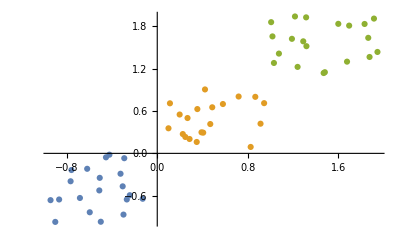

```mathematica
X1=Table[{{1,0,0},RandomReal[{-1,0},2]},{i,20}];
X2=Table[{{0,1,0},RandomReal[{0,1},2]},{i,20}];
X3=Table[{{0,0,1},RandomReal[{1,2},2]},{i,20}];
X11=X1[[;;,2]];
X22=X2[[;;,2]];
X33=X3[[;;,2]];
X=Flatten[{X11,X22,X33},1];
Y=Flatten[{X1[[;;,1]],X2[[;;,1]],X3[[;;,1]]},1]
ListPlot[{X11,X22,X33}]
```

```mathematica
Clear["Global`*"]
```

```mathematica
sigma[x_]:=(1+Exp[-x])^-1
dsigma[x_]:=sigma[x](1-sigma[x])
```

```mathematica
w=Module[{steps=400,η=25,m=Length[X],er={},s=3,s1=2,s2=2,d2,d3,s3=2,g,o,dd1,dd2,i,j,k,w1,w2,iter,z2,z3,y2,y3,y1,b1,b2,db1,db2,dw1,dw2},
w1=RandomReal[{-.1,0.1},{2,2}];
w2=RandomReal[{-.1,0.1},{2,2}];
b1=Table[1,{i,2}];
b2=Table[1,{i,2}];
AppendTo[er,{w1,b1,w2,b2}];
For[iter=1,iter≤steps,iter++,
dw1=Table[0,{i,2},{j,2}];
dw2=Table[0,{i,2},{j,2}];
db1=Table[0,{i,2}];
db2=Table[0,{i,2}];
For[g=1,g≤m,g++,
y1=X[[g]];
z2=Table[Sum[w1[[i,j]]y1[[j]],{j,1,s1}]+b1[[i]],{i,1,s2}];
y2=sigma[z2];
z3=Table[Sum[w2[[i,j]]y2[[j]],{j,1,s2}]+b2[[i]],{i,1,s3}];
y3=sigma[z3];
d3=-(Y[[g]][[1;;2]]-y3)*dsigma[z3];
d2=(w2ᵀ.d3)*dsigma[z2];
Table[dw1[[i,j]]+=d2[[i]]y1[[j]],{i,Length[d2]},{j,Length[y1]}];
Table[dw2[[i,j]]+=d3[[i]] y2[[j]],{i,Length[d3]},{j,Length[y2]}];
db1+=d2;
db2+=d3;
];
w2=w2-η/m dw2;
w1=w1-η/m dw1;
b1=b1-η/m db1;
b2=b2-η/m db2;
AppendTo[er,{w1,b1,w2,b2}];
];
{w1,b1,w2,b2,er}]
```

{{{6.87113,6.07176},{3.85871,3.36713}},3,{{{{0.0526423,0.0269932},{-0.0301034,-0.00954412}},{1,1},{{-0.0742229,0.0802553},{0.082228,-0.0540007}},{1,1}},399,{{{6.87113,6.07176},{3.85871,3.36713}},{1},1,{4.07327,-4.06354}}}}
 |  |  |  |

```mathematica
h[x_,W_]:=Module[{a2,a3},
a2=sigma[Table[Sum[W[[1]][[i,j]]x[[j]],{j,1,Length[x]}]+W[[2]][[i]],{i,1,Length[W[[1]]]}]];
sigma[Table[Sum[W[[3]][[i,j]]a2[[j]],{j,1,Length[a2]}]+W[[4]][[i]],{i,1,Length[W[[3]]]}]]]
```

```mathematica
Q[w_]:=1/2 Sum[Norm[(h[X[[i]],w]-Y[[i]][[1;;2]])]^2,{i,1,Length[X]}]
```

```mathematica
w[[5]][[1]]
```

{{{-0.0598556,0.0545118},{0.0986397,-0.0113436}},{1,1},{{-0.0441129,-0.0402879},{0.00498918,0.0642802}},{1,1}}

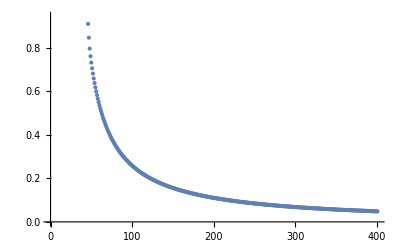

```mathematica
ListPlot[Table[Q[w[[5]][[i]]],{i,1,Length[w[[5]]]}]]
```

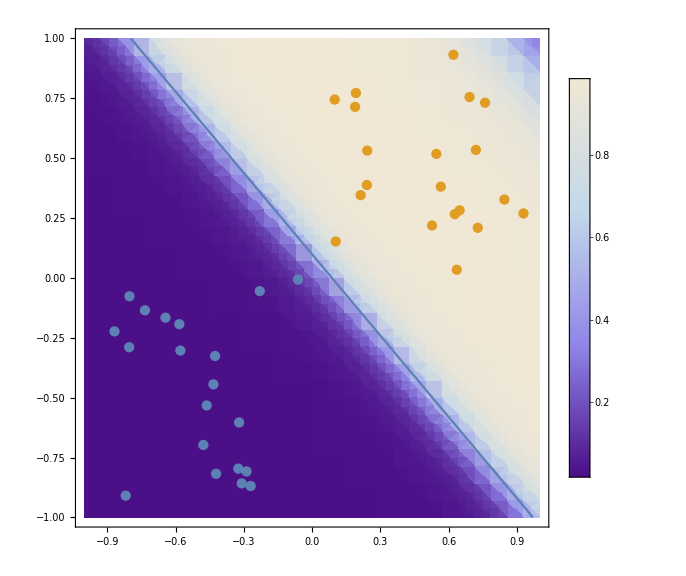

```mathematica
Show[{DensityPlot[h[{x1,x2},w][[2]],{x1,-1,1},{x2,-1,1},PlotLegends->Automatic,ImageSize->Large,PlotTheme->"Classic"],ListPlot[{X11,X22}],ContourPlot[h[{x1,x2},w][[1]]==0.5,{x1,-1,1},{x2,-1,1}]}]
```

```mathematica
Timing[ww=Module[{steps=400,η=20,m=Length[X],er={},s=3,s1=2,s2=4,d2,d3,s3=3,g,o,dd1,dd2,i,j,k,w1,w2,iter,z2,z3,y2,y3,y1,b1,b2,db1,db2,dw1,dw2},
w1=RandomReal[{-.1,.1},{s2,s1}];
w2=RandomReal[{-.1,.1},{s3,s2}];
b1=Table[1,{i,s2}];
b2=Table[1,{i,s3}];
AppendTo[er,{w1,b1,w2,b2}];
For[iter=1,iter≤steps,iter++,
dw1=Table[0,{i,s2},{j,s1}];
dw2=Table[0,{i,s3},{j,s2}];
db1=Table[0,{i,s2}];
db2=Table[0,{i,s3}];
For[g=1,g≤m,g++,
y1=X[[g]];
z2=Table[Sum[w1[[i,j]]y1[[j]],{j,s1}]+b1[[i]],{i,s2}];
y2=sigma[z2];
z3=Table[Sum[w2[[i,j]]y2[[j]],{j,s2}]+b2[[i]],{i,s3}];
y3=sigma[z3];
d3=-(Y[[g]]-y3)*dsigma[z3];
d2=(w2ᵀ.d3)*dsigma[z2];
dw1+=Partition[d2,1].Partition[y1,Length[y1]];
dw2+=Partition[d3,1].Partition[y2,Length[y2]];
(*Table[dw1[[i,j]]+=d2[[i]]y1[[j]],{i,Length[d2]},{j,Length[y1]}];
Table[dw2[[i,j]]+=d3[[i]] y2[[j]],{i,Length[d3]},{j,Length[y2]}];*)
db1+=d2;
db2+=d3;
];
w2=w2-η/m dw2;
w1=w1-η/m dw1;
b1=b1-η/m db1;
b2=b2-η/m db2;
AppendTo[er,{w1,b1,w2,b2}];
];
{w1,b1,w2,b2,er}]]
```

{7.6875,{{{1.29724,2.61043},{-4.3149,-5.34004},{-2.51263,-4.49393},{-2.71989,-3.4138}},{1},{1},{1},{1}}}
 |  |  |  |

```mathematica
h[X[[45]],ww]
```

{0.0107516,0.0172379,0.984771}

```mathematica
Q1[w_]:=1/2 Sum[Norm[(h[X[[i]],w]-Y[[i]])]^2,{i,1,Length[X]}]
```

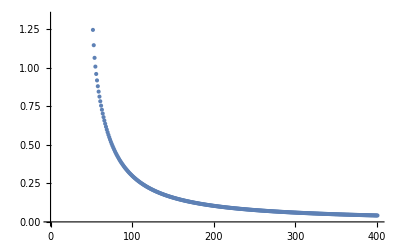

```mathematica
ListPlot[Table[Q1[ww[[5]][[i]]],{i,1,Length[ww[[5]]]}]]
```

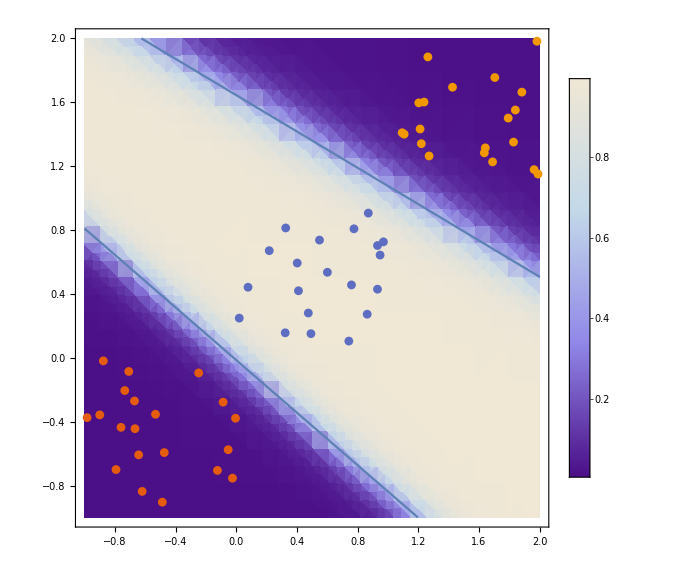

```mathematica
Show[{DensityPlot[h[{x1,x2},ww][[2]],{x1,-1,2},{x2,-1,2},PlotLegends->Automatic,ImageSize->Large,PlotTheme->"Classic"],ListPlot[{X11,X22,X33},PlotTheme->"Scientific"],ContourPlot[h[{x1,x2},ww][[2]]==0.5,{x1,-1,2},{x2,-1,2}]}]
```